```mathematica
ClearAll["Global`*"]
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* import nodes and triangles *)
nodes=Import["nGood.dat","Table"];
(* Mathematica counts from 1 not 0 *)
triangles=Import["tGood.dat","Table"]+1;
elements=Triangle/@triangles; (* map Triangles[] at each element of list of triangles *)
𝒦=MeshRegion[nodes,elements];
nodes=Import["nGoodIni.dat","Table"];
triangles=Import["tGoodIni.dat","Table"]+1;
elements=Triangle/@triangles; (* map Triangles[] at each element of list of triangles *)
Subscript[𝒦, ini]=MeshRegion[nodes,elements];
```

```mathematica
nodes=Import["nBad.dat","Table"];
triangles=Import["tBad.dat","Table"]+1;
elements=Triangle/@triangles;
ℳ=MeshRegion[nodes,elements];
nodes=Import["nBadIni.dat","Table"];
triangles=Import["tBadIni.dat","Table"]+1;
elements=Triangle/@triangles;
Subscript[ℳ, ini]=MeshRegion[nodes,elements];
```

```mathematica
Subscript[Ω, 1]=ImplicitRegion[-1<x<1&&0<y<1-x^2,{x,y}];
Subscript[Ω, 2]=ImplicitRegion[-1<x<0&&-Sqrt[1/4-(x+1/2)^2]<y<0,{x,y}];
Ω=RegionPlot@RegionUnion[Subscript[Ω, 1],Subscript[Ω, 2]];
```

```mathematica
header={"Mesh","Min quality measure of Δ’s","Mean quality measure of Δ’s"};
data=Import["quality.dat","List"];
K ={"𝒦",data[[1]],data[[2]]};
M={"ℳ",data[[3]],data[[4]]};
table=Grid[{header,K,M},Frame->All,Spacings-> {1,1}];
```

(1) Curvilinear region
Our meshes are supposed to approximate it taking curvature into account

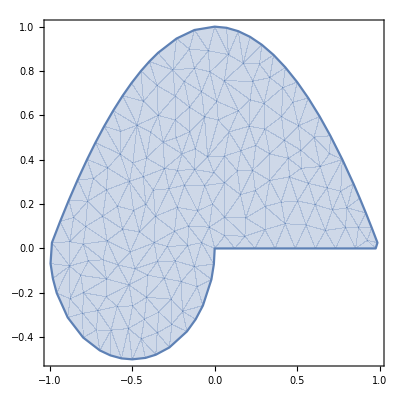

```mathematica
Show[Ω]
```

(2) “Good” mesh
Initial data:

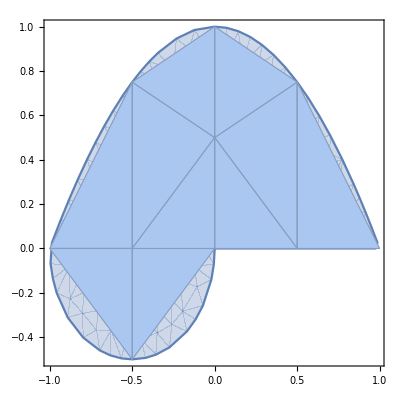

```mathematica
Show[Ω,Subscript[𝒦, ini]]
```

Mesh after 3 uniform refinements:

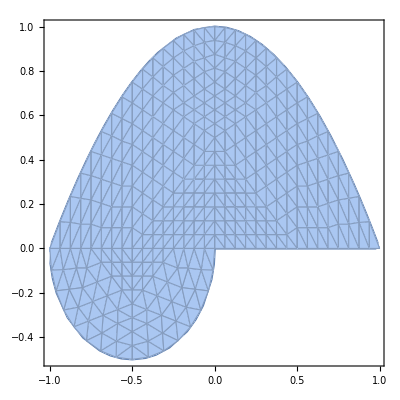

```mathematica
Show[Ω,𝒦]
```

(3) “Bad” mesh
Initial data:

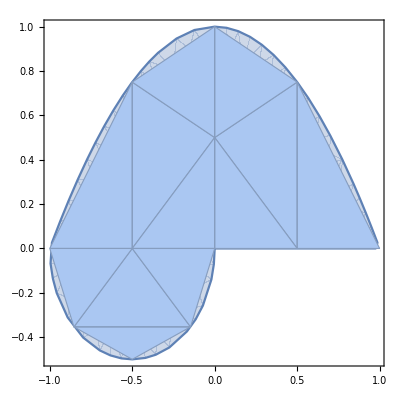

```mathematica
Show[Ω,Subscript[ℳ, ini]]
```

Mesh after 3 uniform refinements:

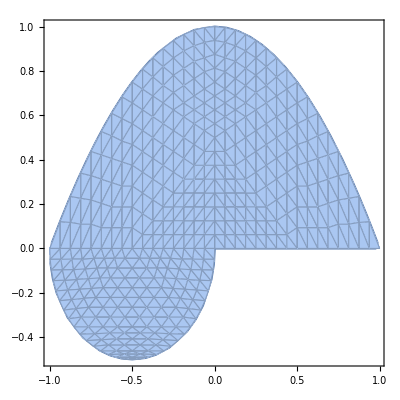

```mathematica
Show[Ω,ℳ]
```

(4) Quality measure of meshes
Indeed, a priori errors of FEM depend on meshes’ quality.
We define quality of triangle as

q_(Δ ∈ Mesh):= √3 d_Δ/h_Δ,d_Δ:=diameter of inscribed circle,h_Δ:=length of the londest edge.

So 0<q_Δ≤1, ideal triangles have measure unity, poor (“skinny”) triangles have very small measure.
It is clear now that mesh ℳ is much poorer (in terms of q_Δ) than 𝒦.

```mathematica
Print[table]
```

Mesh | Min quality measure of Δ’s | Mean quality measure of Δ’s
𝒦 | 0.601478 | 0.810963
ℳ | 0.0425195 | 0.76577